# How does the temperature-size rule affect consumer-resource dynamics?

## MST group project

## Recreating Gilbert

Equations 1 and 2 from Gilbert et al 2014 (with potential temperature dependencies added)

```mathematica
dRdt[R_,C_,T_]:=r[T] R(1-R/K[T])-f[R,T] R C;
dCdt[R_,C_,T_]:=e f[R,T]R C-m[C,T]C;
```

where R is biomass of resource, C is biomass of consumer, T is temperature, K is resource carrying capacity, f is the functional response, e is the conversion efficiency of resources into new consumers, and m is consumer mortality.

BCR at a given T, as defined by Gilbert (Eqn 5),

```mathematica
BCR[T_]:=(e a[T]K[T])/m[T]
```

Equilibrium biomasses at given temperature assuming a type I functional response and density-independent consumer mortality (as in most of Gilbert)

```mathematica
Eq[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR[T_]:=C/R/.Eq[T][[3]]
```

The Jacobian evaluated at equilibrium (determines stability)

```mathematica
Jac={{D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]}}/.Eq[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda=Eigenvalues[Jac];
```

Use Table 1 of Gilbert. Want K=100 at 15 degrees C (Figure 3 of Gilbert), so we need K0 to be

```mathematica
K15=Solve[100==K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T/.T->273.15+15,K0];
```

Figure 3a of Gilbert (same shape but numbers too large)

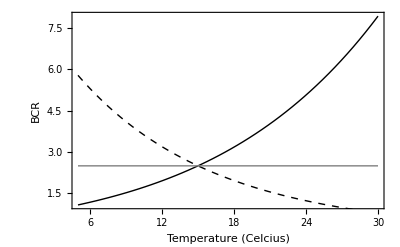

```mathematica
Show[
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thick,Dashed}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Figure 3b of Gilbert (off by factor of 3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

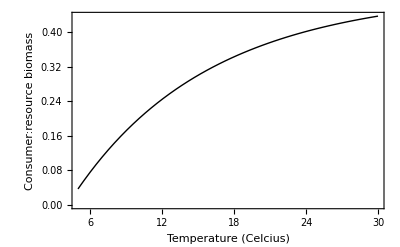

```mathematica
Show[Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"}
]
```

Figure 3c of Gilbert

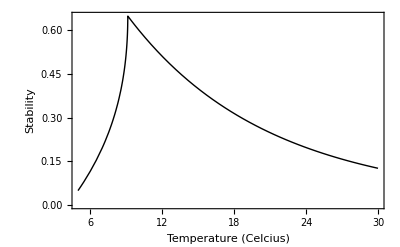

```mathematica
Show[Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"}
]
```

## Adding mass-dependence and the TSR to Gilbert

Now we want to add the body mass relations given in Table 1 of DeLong et al. 2015.

Temperature dependencies of rates given in Table 1 of Gilbert et al. (now letting the constant depend on body mass M)

```mathematica
cr={C,R};
GilbertTable1={
r[T]->r[M] Exp[-EB/(k T[R])],
K[T]->K[M] Exp[EB/(k T[R])-ES/(k T[S])],
m[T]->m[M] Exp[-Em/(k T[C])],
a[T]->a[M] Sqrt[Sum[(ν0[cr[[i]]] Exp[-Eν[cr[[i]]]/(k T[cr[[i]]])])^2,{i,1,Length[cr]}]],
e->e[M]
};
```

Body mass dependencies from DeLong et al.

```mathematica
DeLongTable1={
r[M]->r0 M[R]^ρ,
K[M]->K0 M[R]^κ,
a[M]->a0 M[C]^α,
e[M]->e0 M[C]^ϵ,
m[M]->m0 M[C]^μ
};
```

The temperature-size rule (from Forster et al. 2012), for unicells (e.g., algae)

```mathematica
TSR=M[i_]->M15(1-d (T-15));
```

where d is the percent decrease in mass with a one degree increase from 15 degrees.

What does mass at 15 C need to be to have K=100 at T=15 C (to stay consistent with Gilbert)

```mathematica
m15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->T+273.15/.T->15,M15]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{M15→1. 100.^(1/κ) (ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k)/K0)^(1/κ)}}

Figure 3a of Gilbert (new predictions in red; new dashed curve and horizontal line are now on the order of 10^10 and 10^20 and so do not appear in plot)

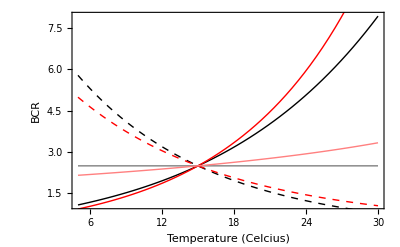

```mathematica
Show[
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thick,Dashed}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thick}],
Plot[Simplify[BCR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.TSR/.m15/.k->8.62*10^-5/.κ->-0.81/.EB->0.32/.ES->0.9/.d->0.02,K0>0],{T,5,30},PlotStyle->{Red,Thick}],
Plot[Simplify[BCR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.TSR/.m15/.k->8.62*10^-5/.κ->-0.81/.EB->0.9/.ES->0.32/.d->0.02,K0>0],{T,5,30},PlotStyle->{Red,Thick,Dashed}],
Plot[Simplify[BCR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.TSR/.m15/.k->8.62*10^-5/.κ->-0.81/.EB->0.9/.ES->0.9/.d->0.02,K0>0],{T,5,30},PlotStyle->{Pink,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Figure 3b of Gilbert (new prediction in red)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

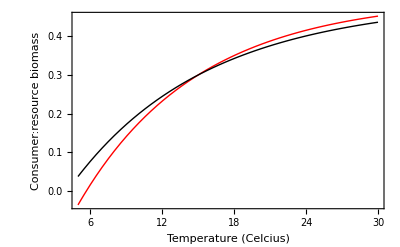

```mathematica
Show[
Plot[Simplify[CR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.TSR/.m15/.k->8.62*10^-5/.κ->-0.81/.EB->0.32/.ES->0.9/.d->0.02,K0>0],{T,5,30},PlotStyle->{Red,Thick}],
Plot[  CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"}
]
```

Figure 3c of Gilbert

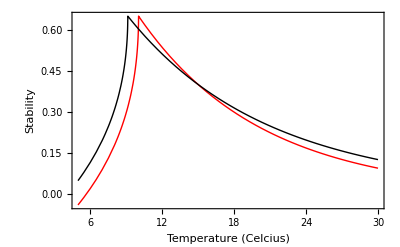

```mathematica
Show[Plot[-Max[Re[Simplify[lambda/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.151/.TSR/.m15/.k->8.62*10^-5/.κ->-0.8/.EB->0.32/.ES->0.9/.d->0.02,K0>0]]]//Chop,{T,5,30},PlotStyle->{Red,Thick}],Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"}
]
```

This only looks at temperature and body mass dependencies in resource carrying capacity K. We next add temperature and mass dependencies to the other rates (and temperature dependence in consumer body mass) to see if this gives bigger discrepancies between the two models.

## Introducing all the dependencies

Let the temperature size rule be linear, but potentially different for resource and consumer

```mathematica
Clear[TSR]
TSR=M[i_]->M15[i](1-β[i](T[i]-(273.15+15)));
```

where M15[i] is the mass of the resource of consumer, i={R,C}, at 15 degrees celcius, β[i] is the percent decline in body size with a degree increase in temperature, and T is the current temperature in Kelvins.

To have the same population dynamics parameter values at 15 degrees as we did above with the TSR only in K, we need

```mathematica
a15=Solve[0.1==a[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 M15[C]^(-1. α))/(√(ⅇ^(-(0.00694083 Eν[C])/k) ν0[C]^2+ⅇ^(-(0.00694083 Eν[R])/k) ν0[R]^2))}

```mathematica
e15=Solve[0.15==e[M]/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

Now, BCR as a function of temperature is

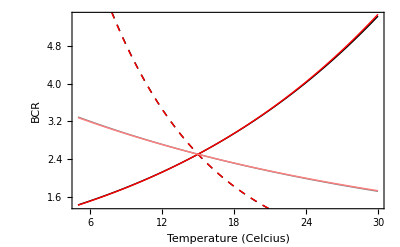

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black,Dashed}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red,Dashed}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Pink}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Nothing much doing here (although notice how the predictions of Gilbert have changed from their Figure 3a, where only K depended on temperature).

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

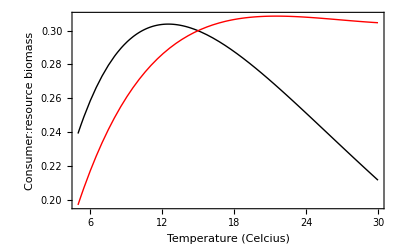

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thick},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thick},Axes->False],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"},
PlotRange->All
]
```

So, the actual prediction of Gilbert et al., when using all the dependencies (not just K, as in Figure 3b), is that the consumer to resource biomass ratio decreases with temperature. However, when we add the TSR we see that the ratio no longer decreases over reasonable temperatures! I.e., temperature directly decreases consumer:resource biomass, but it also decreases body sizes, and decreased body size decreases consumer:resource biomass. In other words, the direct and indirect effects of temperature are of opposite sign.

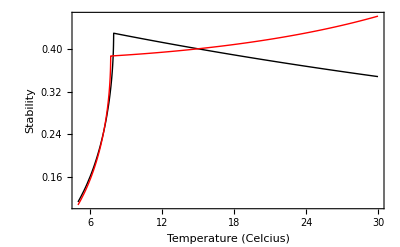

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thick},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"},
PlotRange->All
]
```

With all the dependencies, stability still decreases with temperature (black), albeit slower than when only K depended on temperature (Gilbert Figure 3c). BUT, with the temperature-size rule, stability increases with increasing temperature! Again, temperature directly destabilizes, but indirectly, through its effect on body size, stabilizes the dynamics.

## Exploring asymmetric TSR responses

Until now we’ve supposed that the consumer and resource have the same TSR response. Lets relax that. According to Forster, if the consumer is larger than the resource, it might also have a larger TSR response, say maybe a 3-4% decrease with degree, rather than the 2% for unicells (we are keeping the assumption that the loss is linear).

With a 3% TSR in consumer and a 2% TSR in resource, our predictions become:

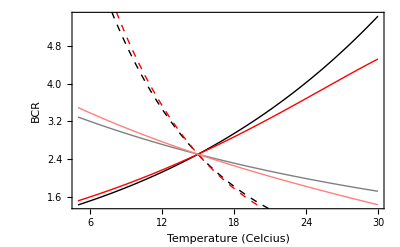

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black,Dashed}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red,Dashed}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Pink}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

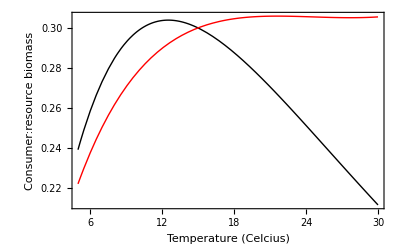

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thick},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thick},Axes->False],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"},
PlotRange->All
]
```

So, the actual prediction of Gilbert et al., when using all the dependencies (not just K, as in Figure 3b), is that the consumer to resource biomass ratio decreases with temperature. However, when we add the TSR we see that the ratio no longer decreases over reasonable temperatures! I.e., temperature directly decreases consumer:resource biomass, but it also decreases body sizes, and decreased body size decreases consumer:resource biomass. In other words, the direct and indirect effects of temperature are of opposite sign.

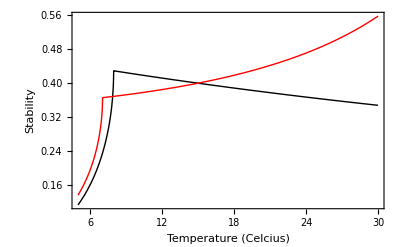

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thick},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"},
PlotRange->All
]
```

With a 4% TSR in consumer and a 2% TSR in resource, our predictions become:

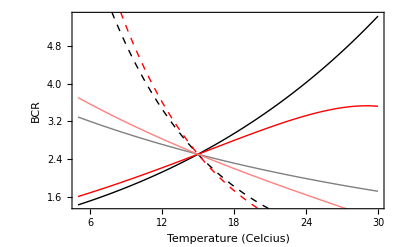

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black,Dashed}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red,Dashed}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Pink}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

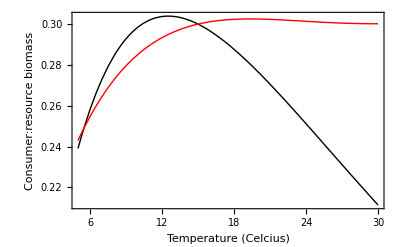

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thick},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thick},Axes->False],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"},
PlotRange->All
]
```

So, the actual prediction of Gilbert et al., when using all the dependencies (not just K, as in Figure 3b), is that the consumer to resource biomass ratio decreases with temperature. However, when we add the TSR we see that the ratio no longer decreases over reasonable temperatures! I.e., temperature directly decreases consumer:resource biomass, but it also decreases body sizes, and decreased body size decreases consumer:resource biomass. In other words, the direct and indirect effects of temperature are of opposite sign.

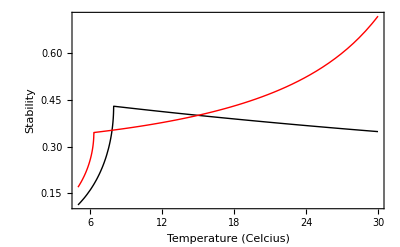

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thick},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"},
PlotRange->All
]
```

So, with a larger TSR response in consumer (as often expected) the dynamics are even further stabilized!

## Making the functional response type-2

BCR at a given T, like that defined by Gilbert (Eqn 5), but with type-ll functional response

```mathematica
BCR2[T_]:=(e f[R,T]K[T])/m[C,T] /.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T]
```

Equilibrium biomasses at given temperature assuming a type Il functional response and density-independent consumer mortality

```mathematica
Eq2[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR2[T_]:=C/R/.Eq2[T][[3]]
```

The Jacobian evaluated at equilibrium (determines stability)

```mathematica
Jac2={{D[dRdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],C]}}/.Eq2[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda2=Eigenvalues[Jac2];
```

Now the dependencies. We can use the scalings of the other parameters from Gilbert and DeLong:

```mathematica
GilbertDeLongT={r[T]->ⅇ^(-EB/(k T[R])) r[M],K[T]->ⅇ^(EB/(k T[R])-ES/(k T[S])) K[M],m[T]->ⅇ^(-Em/(k T[C])) m[M],e->e[M]};
GilbertDeLongM={r[M]->r0 M[R]^ρ,K[M]->K0 M[R]^κ,e[M]->e0 M[C]^ϵ,m[M]->m0 M[C]^μ};
```

The attack rate and handling time scalings are (in a 2D environment; Rall et al. 2012)

```mathematica
RallT={h[T]->ⅇ^(0.65/(k T)) h[M],a[T]->ⅇ^(-0.65/(k T)) a[M]};
RallM={h[M]->h0 M[C]^(-3/4)M[R]^1,a[M]->a0 M[C]^(1/4+1/3)M[R]^(1/3)};
```

To have the same population dynamics parameter values at 15 degrees as Gilbert et al., we need

```mathematica
a152=Solve[0.1==Simplify[a[T]/(1+a[T]h[T]R)/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 1.^(-1.58333+1. ϵ) ⅇ^(0.65/(k T)) e0 M15[C]^(-0.583333+1. ϵ))/(M15[R]^(1/3) (1. e0 M15[C]^ϵ-1. 1.^(-0.75+μ) ⅇ^(-(0.00347041 Em)/k+0.65/(k T)) h0 m0 M15[C]^(-0.75+μ) M15[R]))}

```mathematica
e15=Solve[0.15==e[M]/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

We can set h0 by asking what it needs to be to have BCR with a type-2 equal the BCR with a type-1 at 5 degrees C (this is rather arbitrary!): (CHANGE THIS, BUT TO WHAT?)

```mathematica
h5=Solve[(BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15/.T->5)==(Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+T/.T->5),h0]
```

{{h0→-(2.0222×10^-12 M15[C]^(3/4))/M15[R]}}

Now, BCR as a function of temperature is

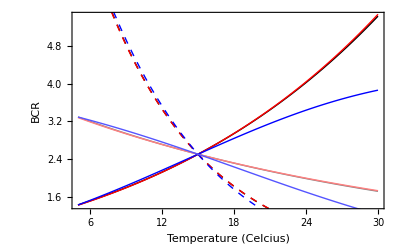

```mathematica
Show[
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thick}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thick,Dashed}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Gray,Thick}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red,Dashed}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Pink}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.h5,{t,5,30},PlotStyle->{Blue,Thick}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.h5,{t,5,30},PlotStyle->{Blue,Thick,Dashed}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.h5,{t,5,30},PlotStyle->{Lighter[Blue],Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Where all parameters are dependent on temperature and/or mass. Black is Gilbert (only temperature dependencies), Red is mass and temp dependencies with type-1 and Blue is mass and temp dependencies with type-2.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

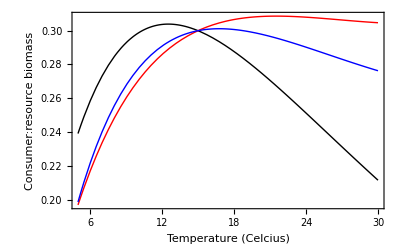

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thick},Axes->False,PlotRange->{0,All}],
Plot[Simplify[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.h5],{t,5,30},PlotStyle->{Blue,Thick},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"},
PlotRange->All
]
```

So, the actual prediction of Gilbert et al., when using all the dependencies (not just K, as in Figure 3b), is that the consumer to resource biomass ratio decreases with temperature. However, when we add the TSR we see that the ratio no longer decreases over reasonable temperatures! I.e., temperature directly decreases consumer:resource biomass, but it also decreases body sizes, and decreased body size decreases consumer:resource biomass. In other words, the direct and indirect effects of temperature are of opposite sign.

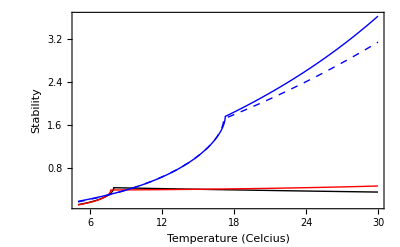

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thick},PlotRange->{0,All}],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.h5/.M15[i_]->100]],{t,5,30},PlotStyle->{Blue,Thick},PlotRange->{0,All}],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.a152/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0/.T->273.15+t/.h5/.M15[i_]->100]],{t,5,30},PlotStyle->{Blue,Thick,Dashed},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"},
PlotRange->All
]
```

Note: even though we have to give M15[i]s to produce blue curve, the result does not (seem to) depend on them.

Why dont things line up at 5 and 15 degrees anymore? Maybe because we are only looking at the Real parts?

Anyways, if this is right, then the type-2 with TSR is by far the most stable, especially at high temperatures.
Type-2 without the TSR is blue dashed; we see that things are generally more stable with a type-2 response, and that the TSR adds extra stability at warm temperatures.

## Improving Rall’s fit

Response of attack rate to temperature, with and without the TSR:

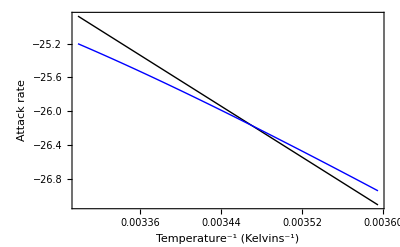

```mathematica
Show[
Plot[Log[a[T]/a0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thick}],
Plot[Log[a[T]/a0]/.RallT/.RallM/.TSR/.T[i_]->T/.k->8.62*10^-5/.M15[i_]->1/.β[i_]->0.02/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thick}],
Plot[Log[ⅇ^(-0.4/(k T)) M[C]^(7/12) M[R]^(1/3)]/.k->8.62*10^-5/.M[i_]->1/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->Orange],
Frame->True,
FrameLabel->{"Temperature^-1 (Kelvins^-1)","Attack rate"}
]
```

The TSR lowers the activation energy of attack rate, which goes in the same direction as the discrepancy seen in Rall (see Figure 3a in Rall et al 2012).

And for handling time:

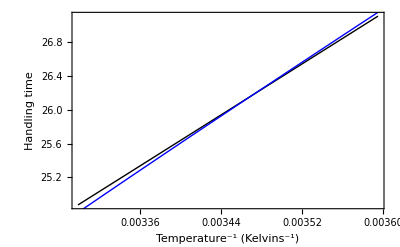

```mathematica
Show[
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thick}],
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.TSR/.T[i_]->T/.M15[i_]->1/.β[i_]->0.02/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thick}],
Frame->True,
FrameLabel->{"Temperature^-1 (Kelvins^-1)","Handling time"}
]
```

Here the TSR (slightly) increases the activation energy of handling time. But this is with same TSR in resource and consumer. If we allow the consumer to have a larger TSR, then we have

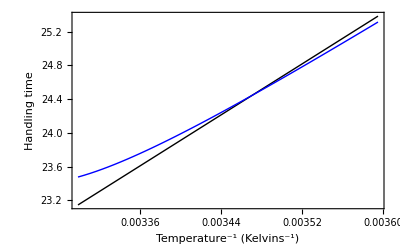

```mathematica
Show[
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.M[R]->1/.M[C]->10/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thick}],
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.TSR/.T[i_]->T/.M15[R]->1/.M15[C]->10/.β[R]->0.02/.β[C]->0.04/.T->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thick}],
Frame->True,
FrameLabel->{"Temperature^-1 (Kelvins^-1)","Handling time"}
]
```

which makes the activation energy of handling time smaller, as in Rall (see Figure 3d).

## Effect of the TSR on the functional response

This section is based on Kalinkat et al. 2013.

In particular, we let the functional response be

```mathematica
g[R_,T_]:=(b[T] R^q[M])/(1+h[T]b[T] R^(1+q[M]))
```

such that when q=0 we have a type-1 functional response and when q>0 we have a type-3 (sigmiodal):

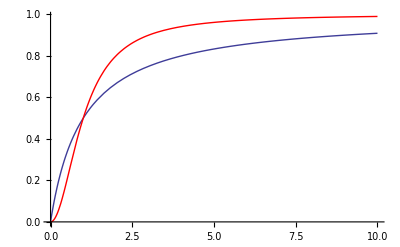

```mathematica
Show[
Plot[g[R,T]R/.b[T]->1/.h[T]->1/.q[M]->0,{R,0,10},PlotRange->{0,All}],
Plot[g[R,T]R/.b[T]->1/.h[T]->1/.q[M]->1,{R,0,10},PlotRange->{0,All},PlotStyle->Red],
PlotRange->{0,All}
]
```

We say q is a function of mass M, because it depends on the ratio of consumer to resource body size

```mathematica
q[M_]:=(qmax (M[C]/M[R])^2)/(q0^2+(M[C]/M[R])^2)
```

where qmax and q0 are scaling parameters that determine the shape of the sigmoidal response (qmax is the asymptote, q0^2 is the half-saturation constant):

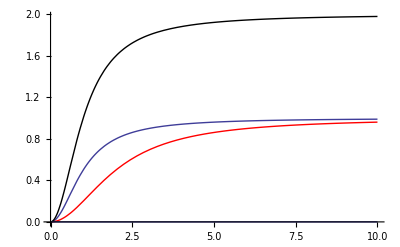

```mathematica
Show[
Plot[q[M]/.M[C]->a M[R]/.qmax->1/.q0->1,{a,0,10},PlotRange->{0,All}],
Plot[q[M]/.M[C]->a M[R]/.qmax->1/.q0->2,{a,0,10},PlotRange->{0,All},PlotStyle->Red],
Plot[q[M]/.M[C]->a M[R]/.qmax->2/.q0->1,{a,0,10},PlotRange->{0,All},PlotStyle->Black],
Plot[q[M]/.M[C]->a M[R]/.qmax->3.3/.q0->10^3,{a,0,10},PlotRange->{0,All},PlotStyle->Thick]
]
```

The fitted values in Kalinkat give the following curve

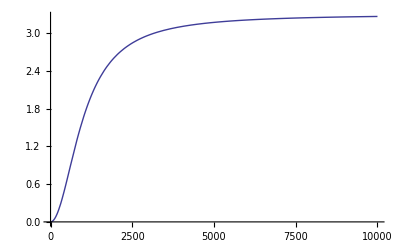

```mathematica
Plot[q[M]/.M[C]->a M[R]/.qmax->3.3/.q0->10^3,{a,0,10^4},PlotRange->{0,All},PlotStyle->Thick]
```

What effect does the TSR have on q?

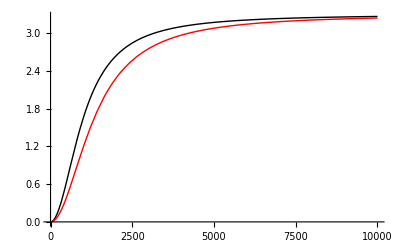

```mathematica
Show[
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0/.β[C]->0/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Black],
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0.02/.β[C]->0.04/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Red]
]
```

As we might expect, because q depends on the ratio of body sizes, if both resource and consumer have the same TSR, then the TSR has no affect on q. 
However, when the consumer has a larger TSR than the resource, the body size ratio decreases with temperature, decreasing q and therefore slowing the switch from type-2 to type-3.
Because type-3 is more stable, the TSR may be said to reduce stability by this mechanism (as we can see in the above plot, with the TSR (red) q is not reduced by much).

## Indirect effect only

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

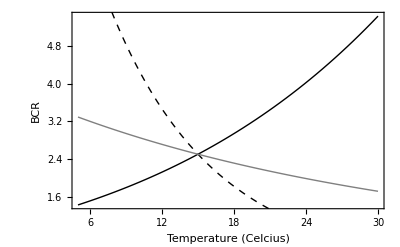

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black,Dashed}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->0/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->0/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red,Dashed}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->0/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Pink}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Nothing much doing here (although notice how the predictions of Gilbert have changed from their Figure 3a, where only K depended on temperature).

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thick},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thick},Axes->False],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"},
PlotRange->All
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics-

So, the actual prediction of Gilbert et al., when using all the dependencies (not just K, as in Figure 3b), is that the consumer to resource biomass ratio decreases with temperature. However, when we add the TSR we see that the ratio no longer decreases over reasonable temperatures! I.e., temperature directly decreases consumer:resource biomass, but it also decreases body sizes, and decreased body size decreases consumer:resource biomass. In other words, the direct and indirect effects of temperature are of opposite sign.

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thick},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"},
PlotRange->All
]
```

-Graphics-